```mathematica
(*Mathematica*)
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:=(x/(1-x))/;0<=x<=1/2
f[x_]:=((1-x)/x)/;1/2<x<=1
```

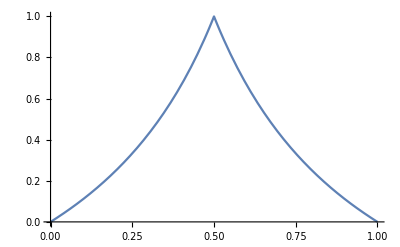

```mathematica
Plot[f[x],{x,0,1}]
```

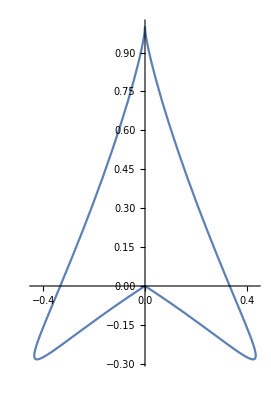

```mathematica
ParametricPlot[{f[x]*Sin[2*Pi*x],(1-f[x])*Cos[2*Pi*x]},{x,0,1}]
```

```mathematica
f[Re[z]]+I*f[Im[z]]
```

ⅈ f[Im[z]]+f[Re[z]]

```mathematica
(*Farey complex Plot*)
```

```mathematica
ComplexPlot[f[Re[z]]+I*f[Im[z]],{z,-0.1-0.1*I,1.1+1.1*I},ColorFunction->"CyclicReImLogAbs",ImageSize->Full]
```

-Graphics-

```mathematica
(*Farey 2d Cylinder*)
```

```mathematica
(*ParametricPlot3D[{f[x]*Sin[2*Pi*x],f[y]*Sin[2*Pi*x],Cos[2*Pi*x]},{x,0,1},{y,0,1},ColorFunction->Hue,ImageSize->Full]*)
```

```mathematica
(*3d Product projection of Farey function*)
```

```mathematica
g1=ParametricPlot3D[{(f[x]*Sin[2*Pi*x])*(1-f[y])*Cos[2*Pi*y],(f[x]*Sin[2*Pi*x])*f[y]*Sin[2*Pi*y],(1-f[x])*Cos[2*Pi*x]},{x,0,1},{y,0,1},ColorFunction->Hue,ImageSize->{2000,2000},Mesh->False,Boxed->False,PlotPoints->100,Background->Black,PlotRange->All];
```

```mathematica
g2=Show[g1,ImageSize->{2000,2000},ViewPoint->{2,2,2}];
```

```mathematica
g3=Show[g1,ImageSize->{2000,2000},ViewPoint->Front];
```

```mathematica
g4=Show[g1,ImageSize->{2000,2000},ViewPoint->{2,1.3,-2.4}];
```

```mathematica
Export["Farey_Delta_surface_grid2.jpg",GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->{{4000},{4000}}]]
```

Farey_Delta_surface_grid2.jpg

```mathematica
Export["Farey_Delta_surface.ply",g1]
```

Farey_Delta_surface.ply

```mathematica
(*end*)
```